## Shooting Method Solution

### Pick potential

```mathematica
V[ϕ_,α_]:=ϕ^2/2+ϕ^3/2+α ϕ^4/8;
```

### Pretty Plot

```mathematica
PrettyPlot[scheme_]:=(
αs={95/100,85/100,75/100,65/100,55/100,45/100};
ts ={{-2.9,0.4471},{-3.323,-0.2307},{-4.129,-1.496},{-4.99,-2.942},{-6.205,-5.269},{-8.363,-7.415}};
ticks[min_,max_]:=Join[Table[{i,Style[i,14],{.02,0}},{i,Ceiling[min],Floor[max]}],Table[{j+.5,,{.01,0}},{j,Round[min],Round[max-1],1}]];
ticks2[min_,max_]:=Join[Table[{i,Style[i,14],{.02,0}},{i,Ceiling[min],Floor[max]}],Table[{j+.5,,{.01,0}},{j,Round[min],Round[max-1],2}]];
Show[
Table[
Plot[V[ϕ,α],{ϕ,-100,1},PlotRange->{{-8.5,0.5},{-8.1,1.1}},Axes->False,Frame->True,PlotStyle->Directive[{Thick,ColorData[scheme][α*1.95-0.87]}],ImageSize->700,FrameLabel->(Style[#,FontSize->27]&/@{"ψ","V̄(ψ)"}),FrameTicks->True,FrameTicksStyle->Directive[18]]
,{α,αs}
]
(*,Plot[0,{x,-100,1},PlotStyle->Black]*)
,Graphics[Table[{Darker[ColorData[scheme][α*1.95-0.87]],Text[Style["α="<>ToString[N[α,2]],FontSize->21],ts⟦Position[αs,α]⟦1,1⟧⟧,{-1,-1}]},{α,αs}]]
(*,Graphics[Table[Point[{(-3-√(9-8 α))/(2 α),V[(-3-√(9-8 α))/(2 α),α]}],{α,αs}]]*)
]
)
PrettyPlot["DarkRainbow"]
```

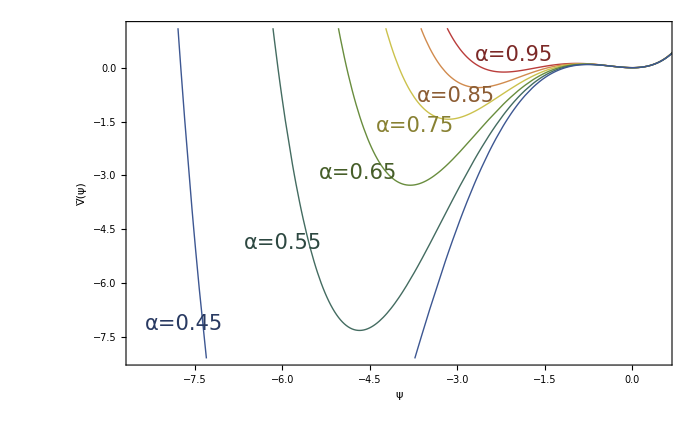

### Solution Parameters

```mathematica
SetParams[]:=(
size=1000;
xmin = 10^-100; xmax =  12 1/(1-α); δx=(xmax-xmin)/size;
xgrid=Table[x,{x,xmax,xmin,-δx}];

revstep = ϕm/.Solve[(ϕp+ϕm-2ϕ)/δx^2+2/ρ(ϕp-ϕm)/(2δx)-D[V[ϕ,α],ϕ]==0,ϕm]⟦1⟧;
fevstep = ϕp/.Solve[(ϕp+ϕm-2ϕ)/δx^2+2/ρ(ϕp-ϕm)/(2δx)-D[V[ϕ,α],ϕ]==0,ϕp]⟦1⟧;
RGetSolution[δ_] :=(
ϕsol=SetPrecision[{0,δ},precision];
Do[
If[Abs[ϕsol⟦-1⟧]>10^10,0;,AppendTo[
ϕsol,
N[(revstep/.{ϕ->ϕsol⟦-1⟧,ϕp->ϕsol⟦-2⟧,ρ->xgrid⟦i⟧}),precision]
]
];,{i,Length[xgrid]-1}
];
Return[ϕsol];
);
FGetSolution[g_,δ_] :=(
ϕsol=SetPrecision[{g,g+δ},precision];
Do[
If[Abs[ϕsol⟦-1⟧]>10^10,0;,AppendTo[
ϕsol,
N[(fevstep/.{ϕ->ϕsol⟦-1⟧,ϕm->ϕsol⟦-2⟧,ρ->xgrid⟦-i⟧}),precision]
]
];,{i,Length[xgrid]-1}
];
Return[ϕsol];
);
);
SetParams[];
```

### Manual Solution

```mathematica
precision = 800;
range=1+10^1;
δguess =-13/10*10^-11;
Manipulate[
ϕsol=RGetSolution[δ];
Quiet[Show[
ListPlot[Transpose[{xgrid⟦1;;Length[ϕsol]-1⟧,ϕsol⟦2;;⟧}],Axes->False,Frame->True,Joined->True,PlotRange->{All,{(1+1/10) (-3-√(9-8 α))/(2 α),(-3-√(9-8 α))/(2 α)/-10}},PlotStyle->Directive[Thick,Green],ImageSize->500,PlotLabel->{N[ϕsol⟦-1⟧,20],N[δ,20]}],
Plot[{0,(-3-√(9-8 α))/(2 α),(-3+√(9-8 α))/(2 α)},{x,0,xmax}]
]],{{δ,δguess},δguess/range, range δguess,δguess (range-1)/100}
]
```

```mathematica
precision = 800;
range=1+10^2;
δguess = 10^-12;
ιguess=-328/100;
Manipulate[
ϕsol=FGetSolution[ι,δ];
Quiet[Show[
ListPlot[Transpose[{Reverse[xgrid⟦1;;Length[ϕsol]-1⟧],ϕsol⟦;;-2⟧}],Axes->False,Frame->True,Joined->True,PlotRange->{All,{(1+1/10) (-3-√(9-8 α))/(2 α),(-3-√(9-8 α))/(2 α)/-10}},PlotStyle->Directive[Thick,Green],ImageSize->500,PlotLabel->{N[ϕsol⟦-1⟧,20],N[δ,20]}],
Plot[{0,(-3-√(9-8 α))/(2 α),(-3+√(9-8 α))/(2 α)},{x,0,xmax}]
]],{{δ,δguess},δguess/range, range δguess,δguess (range-1)/20},{ι,-30110/10000,-34112/10000}
]
```

### Automatic Solution

#### Function

```mathematica
α=0.95
GetSol[]:=(
precision = 800;
tol=10^-450;
maxiter=1000; iter=0;
δmin = 0;
δmax = -10^-1;

(* phase 1: get near the solution - find where the derivative flips sign *)
While[Round[δmax,10 tol]≠ Round[δmin,10 tol] && iter<maxiter,(
δguess=(δmax+δmin)/2;
(* look at derivative *)
ϕder=(#⟦-2⟧-#⟦-3⟧)&@RGetSolution[δguess];
If[ϕder>0,
δmax=δguess;,
δmin=δguess;
];
iter++;
)];
Print[N[{δmin,δmax,δguess,iter,ϕder}]]

(* phase 2: Extra accuracy - search near the solution *)
(*δmax=1.0001δguess;
δmin=δguess/1.0001;
While[Round[δmax,tol/10]≠ Round[δmin,tol/10] && iter<maxiter,(
δguess=(δmax+δmin)/2;
(* look at derivative *)
ϕder=(#⟦-1⟧-#⟦-2⟧)&@RGetSolution[δguess];
If[ϕder<0,
δmax=δguess;,
δmin=δguess;
];
iter++;
)];
Print[N[{δmin,δmax,δguess,iter,ϕder}]]
*)
);
```

0.95

#### Sample Solution

0.95

{-6.59609×10^-100,-6.59609×10^-100,-6.59609×10^-100,1000.,3.6729×10^-8}

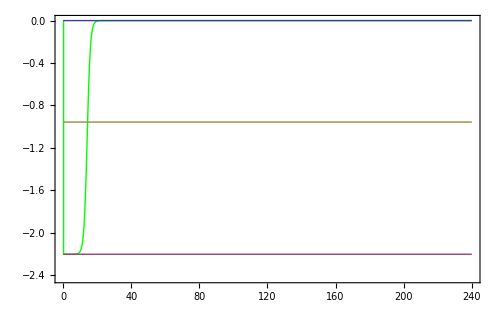

```mathematica
SetParams[];
GetSol[];
Quiet[Show[
ListPlot[Transpose[{xgrid⟦1;;Length[ϕsol]-1⟧,ϕsol⟦2;;⟧}],Axes->False,Frame->True,Joined->True,PlotRange->{All,{1.1(-3-√(9-8 α))/(2 α),0}},PlotStyle->Directive[Thick,Green],ImageSize->500],
Plot[{0,(-3-√(9-8 α))/(2 α),(-3+√(9-8 α))/(2 α)},{x,0,xmax}]
]]
```

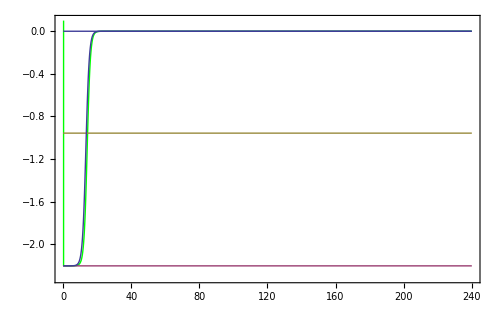

```mathematica
Quiet[Show[
ListPlot[Transpose[{xgrid⟦1;;Length[ϕsol]-1⟧,ϕsol⟦2;;⟧}],Axes->False,Frame->True,Joined->True,PlotRange->{All,{1.05(-3-√(9-8 α))/(2 α),0.1}},PlotStyle->Directive[Thick,Green],ImageSize->500],
Plot[{0,(-3-√(9-8 α))/(2 α),(-3+√(9-8 α))/(2 α)},{x,0,xmax}],
Plot[(3+√(9-8 α))/(4 α)(Tanh[1/2(ρ-2/3 1/(1-α))]-1),{ρ,0,xmax},PlotRange->All]
]]
```

#### Get Range of Solutions From α list in pretty potential plot

```mathematica
sols={};
Do[
α=a;
SetParams[];
GetSol[];
AppendTo[sols,Transpose[{xgrid⟦1;;Length[ϕsol]-1⟧,ϕsol⟦2;;⟧}]];
,{a,αs}
]
```

{-6.59609×10^-100,-6.59609×10^-100,-6.59609×10^-100,1000.,5.16011×10^-199}

{-6.41948×10^-35,-6.41948×10^-35,-6.41948×10^-35,1000.,1.5156×10^-266}

{-5.46938×10^-22,-5.46938×10^-22,-5.46938×10^-22,1000.,-2.53341×10^-281}

{-1.79015×10^-16,-1.79015×10^-16,-1.79015×10^-16,1000.,-1.85319×10^-285}

{-2.01623×10^-13,-2.01623×10^-13,-2.01623×10^-13,1000.,-1.45125×10^-288}

{-1.73268×10^-11,-1.73268×10^-11,-1.73268×10^-11,1000.,8.66351×10^-291}

```mathematica
ts2 ={{19.65,-1.675},{5.458,-2.213},{2.443,-2.684},{1.559,-3.09},{1.04,-3.43},{0.7277,-3.877}};
ticksx[min_,max_]:=Join[Table[{i,Style[i,14],{.02,0}},{i,Ceiling[min],Floor[max],10}],Table[{j+5,,{.01,0}},{j,Round[min],Round[max-1],10}]]
Show[
Table[
ListPlot[{#⟦1⟧,#⟦2⟧/((3+√(9-8 α))/(2 α))}&/@sols⟦Position[αs,α]⟦1,1⟧⟧⟦;;-2⟧,Joined->True,PlotRange->{{0,30},{-1.1,0.1}},Axes->False,Frame->True,PlotStyle->Directive[{Thick,ColorData["DarkRainbow"][α*1.95-0.87]}],ImageSize->700,FrameLabel->(Style[#,FontSize->27]&/@{"ρ̄","ψ(ρ̄)/ψ_-"}),FrameTicks->{{ticks,None},{ticksx,None}}]
,{α,Reverse[αs]}
],
Plot[0,{x,-100,1},PlotStyle->Black],
Graphics[Table[{Darker[ColorData["DarkRainbow"][α*1.95-0.87]],Text[Style["α="<>ToString[N[α,2]],FontSize->21],{10,-.5},{-1,1}]},{α,αs}]]
]
```

#### Export Solution

```mathematica
bubblefn=Interpolation[N[Join[{{0,ϕsol⟦-1⟧}},Transpose[{xgrid⟦1;;Length[ϕsol]-1⟧,ϕsol⟦2;;⟧}]]]];
```

```mathematica
Plot[bubblefn[x],{x,0,5 R0}]
```

```mathematica
simsize= 512;
b={-3.^(-1/2)xmax,3.^(-1/2)xmax,2 3.^(-1/2) xmax/simsize};
data=Table[bubblefn[Sqrt[x^2+y^2+z^2]],{x,b⟦1⟧,b⟦2⟧,b⟦3⟧},{y,b⟦1⟧,b⟦2⟧,b⟦3⟧},{z,b⟦1⟧,b⟦2⟧,b⟦3⟧}];
```

```mathematica
Table[Point[{(-3.-√(9-8 α))/(2 α),V[(-3.-√(9-8 α))/(2 α),α]}],{α,αs}]
```

{Point[{-2.20169,-0.122212}],Point[{-2.6372,-0.553951}],Point[{-3.1547,-1.43647}],Point[{-3.8072,-3.27437}],Point[{-4.67706,-7.32002}],Point[{-5.91532,-17.1251}]}

### Multiple Bubbles

```mathematica
sols={};
α=0.45; R0=1/(1-α)
SetParams[];
GetSol[];
```

1.81818

{-1.73268×10^-11,-1.73268×10^-11,-1.73268×10^-11,1000.,-4.94715×10^-12}

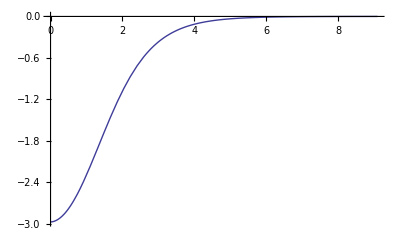

```mathematica
bubblefn=Interpolation[N[Join[{{0,ϕsol⟦-2⟧}},Transpose[{xgrid⟦1;;Length[ϕsol]-2⟧,ϕsol⟦1;;-3⟧}],{{1000,ϕsol⟦1⟧}}]]];
Plot[bubblefn[x],{x,0,5 R0},PlotRange->{{0,5R0},{0,-0.1-3}}]
```

```mathematica
nb=6;
s=18R0;
spacing=5R0;
ModDistance[u_,v_]:=Sqrt[Total[(Mod[Min[Abs[(#1-#2) {1,1,1}+{0,s,-s}]],s]&@@@({u,v}ᵀ))^2]]
```

```mathematica
points={RandomReal[{0,s},3]};
Dynamic[points]
Dynamic[Length[points]]
While[Length[points]<nb,
p=RandomReal[{0,s},3];
If[Min[ModDistance[#,p]&/@points]>spacing,AppendTo[points,p]];
]
Graphics3D[
Table[
{RGBColor[0.,.3,.3,.4],Sphere[(#+{ox,oy,oz}),1.05R0]&/@points,RGBColor[0.,.7,.7,.9],Sphere[(#+{ox,oy,oz}),1. R0]&/@points},
{ox,-s,s,s},{oy,-s,s,s},{oz,-s,s,s}
],PlotRange->{{0,s},{0,s},{0,s}}
]
```

```mathematica
res = 256;
quarterbubble=
Table[bubblefn[√(x^2+y^2+z^2)],{x,0,s/2-s/res,s/res},{y,0,s/2-s/res,s/res},{z,0,s/2-s/res,s/res}];

GridMirror[grid_,level_]:=Join[Reverse[grid,level],grid,level];

fullbubble=GridMirror[GridMirror[GridMirror[quarterbubble,1],2],3];
allbubbles=Total[RotateRight[fullbubble,Round[#/s*res]]&/@points];
```

```mathematica
ListContourPlot3D[
allbubbles,PlotRange->{{0,res},{0,res},{0,res}},Contours->{-.1,-.5,-2.5},Mesh->False
]
```

```mathematica
Export["~/Desktop/INITIAL_a-"<>ToString[N[α,2]]<>"_SIZE-"<>ToString[Round[s/R0]]<>"R0_RES-"<>ToString[res]<>"_BUBBLES-"<>ToString[Length[points]]<>".h5",allbubbles];
```